```mathematica
Dir[p_,n_]:=Module[{a},a=2*Pi*p/n;{Cos[a],Sin[a]}];
Dir[1,2]
```

{-1,0}

```mathematica
Module[
{a,b},
a={0,0};
b=a;
a[[1]]=1;
Print[a];
];
```

{1,0}

```mathematica
Barycenter[places_]:=Module[
{c,m,n},
c={0,0};
m=0;
n=Length[places];
Do[
If[places[[i]]≠0,c+=Dir[i,n];m+=1;],
{i,1,n}
];
c/m
];
Barycenter[{1,1,0}]
```

{-1/2,0}

```mathematica
Place[func_,places_,p_,n_]:=Module[
{np,npf,plc},
np=Length[places];
npf=np-p+1;
plc=places;
If[n==0,
If[Barycenter[plc]=={0,0},func[plc]],
If[npf≥n,
plc[[p]]=1;
Place[func,plc,p+1,n-1];
plc[[p]]=0;
Place[func,plc,p+1,n];
];
];
];
Place[Function[{s},sol=s;Print[s]],
{0,0,0,0,0,0,0,0,0,0,0,0},1,5]
```

{1,1,0,0,1,0,0,1,1,0,0,0}

{1,1,0,0,0,1,1,0,0,1,0,0}

{1,0,0,1,1,0,0,0,1,1,0,0}

{1,0,0,1,0,0,1,1,0,0,0,1}

{1,0,0,0,1,1,0,0,1,0,0,1}

{0,1,1,0,0,1,0,0,1,1,0,0}

{0,1,1,0,0,0,1,1,0,0,1,0}

{0,1,0,0,1,1,0,0,0,1,1,0}

{0,0,1,1,0,0,1,0,0,1,1,0}

{0,0,1,1,0,0,0,1,1,0,0,1}

{0,0,1,0,0,1,1,0,0,0,1,1}

{0,0,0,1,1,0,0,1,0,0,1,1}

{{1/2,(√3)/2},{(√3)/2,1/2},{1,0},{(√3)/2,-1/2},{1/2,-(√3)/2},{0,-1},{-1/2,-(√3)/2},{-(√3)/2,-1/2},{-1,0},{-(√3)/2,1/2},{-1/2,(√3)/2},{0,1}}

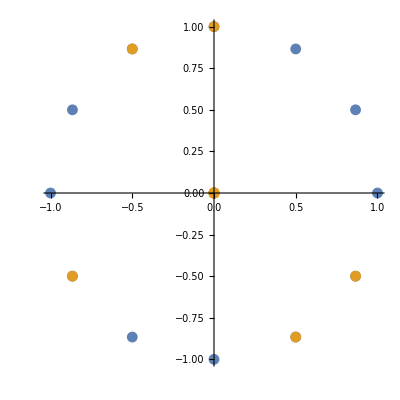

```mathematica
l1=Table[{Sin[2*Pi*i/12],Cos[2*Pi*i/12]},{i,12}]
ListPlot[{l1,l1*sol},AspectRatio->1]
```

```mathematica
a={0,0,0};
n = Table[i,{i,1,Length[a]}];
Do[a[[i]]=Function[{x},x*n[[i]]],{i,1,Length[a]}];
a
```